```mathematica
SetDirectory["/home/bart/DiagHam_Stability/trunk/quartic_2"]
Get["BandGeometryNCnew`"]
```

/home/bart/DiagHam_Stability/trunk/quartic_2

BandGeometry-nocompile v2016-6-29

```mathematica
ClearAll[trIneqTable,detIneqTable,varBerryTable,varGTable]
```

```mathematica
trIneqTable[model_,m_] := Quiet@ParallelTable[{m,t2,Abs@rmsCurvature[{model,1,m,t2}]/(2Pi*m),bzIntegrate[trGInequality,{model,1,m,t2}]/(2Pi m)},{t2,-0.25,0,0.01}]
detIneqTable[model_,m_] := Quiet@ParallelTable[{m,t2,bzIntegrate[detGInequality,{model,1,m,t2}]/(2Pi m)},{t2,-0.25,0,0.01}]
varBerryTable[model_,m_] := Quiet@ParallelTable[{m,t2,Abs@rmsCurvature[{model,1,m,t2}]},{t2,-0.25,0,0.01}]
varGTable[model_,m_] :=  Quiet@ParallelTable[{m,t2,Abs@trRMSMetric[{model,1,m,t2}]},{t2,-0.25,0,0.01}]
```

```mathematica
trIneqTable["QHofstadter",24]
trIneqTable["QHofstadter",54]
```

{{24,-0.25,0.0140393},{24,-0.24,0.0110846},{24,-0.23,0.00874655},{24,-0.22,0.00688563},{24,-0.21,0.00539806},{24,-0.2,0.00420565},{24,-0.19,0.00324872},{24,-0.18,0.00248117},{24,-0.17,0.00186703},{24,-0.16,0.00137798},{24,-0.15,0.00099151},{24,-0.14,0.000689592},{24,-0.13,0.000457681},{24,-0.12,0.000283965},{24,-0.11,0.000158791},{24,-0.1,0.0000742239},{24,-0.09,0.0000237101},{24,-0.08,1.80741×10^-6},{24,-0.07,3.97786×10^-6},{24,-0.06,0.0000264215},{24,-0.05,0.0000659443},{24,-0.04,0.000119852},{24,-0.03,0.000185865},{24,-0.02,0.000262049},{24,-0.01,0.000346756},{24,0.,0.000438582}}

{{54,-0.25,0.0143172},{54,-0.24,0.0093725},{54,-0.23,0.00635963},{54,-0.22,0.00442327},{54,-0.21,0.00312826},{54,-0.2,0.00223567},{54,-0.19,0.00160618},{54,-0.18,0.00115455},{54,-0.17,0.000826479},{54,-0.16,0.000586251},{54,-0.15,0.000409671},{54,-0.14,0.000279963},{54,-0.13,0.000185246},{54,-0.12,0.000116957},{54,-0.11,0.0000688183},{54,-0.1,0.0000361703},{54,-0.09,0.0000155067},{54,-0.08,4.16186×10^-6},{54,-0.07,8.9235×10^-8},{54,-0.06,1.70383×10^-6},{54,-0.05,7.76875×10^-6},{54,-0.04,0.0000173122},{54,-0.03,0.0000295662},{54,-0.02,0.0000439205},{54,-0.01,0.000059888},{54,0.,0.0000770787}}

```mathematica
(*gapVtrace24=MapThread[{#1,#2}&,{Transpose[trace[24]][[2]],Transpose[gapVsDelta24][[2]]}]*)
gapVrmsB=MapThread[{#1,#2}&,{Transpose[varBerry[24]][[2]],Transpose[gapVsDelta24][[2]]}]
gapVrmsG=MapThread[{#1,#2}&,{Transpose[varG[24]][[2]],Transpose[gapVsDelta24][[2]]}]
gapVdetIneq=MapThread[{#1,#2}&,{Transpose[detIneq[24]][[2]],Transpose[gapVsDelta24][[2]]}]
```

```mathematica
gapVtrace24={{1.0140393299749717,1.2153618161798398},{1.0110845885001938,1.21613521600512},{1.0087465540694176,1.2166575396883201},{1.00688562644148,1.2167003218176},{1.0053980581131599,1.2167416826380801},{1.0042056526261436,1.2167814338208},{1.0032487188323098,1.21681937086272},{1.0024811652224987,1.21685526476928},{1.0018670283929194,1.21688886321792},{1.0013779797173898,1.2169198849593599},{1.000991510119412,1.2169480182047998},{1.000689591941018,1.2169729175270398},{1.00045768110974,1.21699419728832},{1.0002839651159454,1.21701142831104},{1.000158790638796,1.2170241308736},{1.0000742239019598,1.2170317702464002},{1.0000237100913805,1.21703374797696},{1.0000018074087853,1.2170293927776},{1.0000039778561738,1.21701795147648},{1.0000264214999242,1.2169985772902399},{1.000065944318145,1.2169703164896},{1.00011985217744,1.2169320923692801},{1.0001858652798894,1.21688268626304},{1.0002620487510703,1.21682071921536},{1.000346756033678,1.2167446229568002},{1.0004385824996438,1.2166526111500802}}
```

{{1.01404,1.21536},{1.01108,1.21614},{1.00875,1.21666},{1.00689,1.2167},{1.0054,1.21674},{1.00421,1.21678},{1.00325,1.21682},{1.00248,1.21686},{1.00187,1.21689},{1.00138,1.21692},{1.00099,1.21695},{1.00069,1.21697},{1.00046,1.21699},{1.00028,1.21701},{1.00016,1.21702},{1.00007,1.21703},{1.00002,1.21703},{1.,1.21703},{1.,1.21702},{1.00003,1.217},{1.00007,1.21697},{1.00012,1.21693},{1.00019,1.21688},{1.00026,1.21682},{1.00035,1.21674},{1.00044,1.21665}}

ListPlot::nonopt: Options expected (instead of Null) beyond position 1 in ListPlot[{{1.01404, 1.21536}, {1.01108, 1.21614}, {1.00875, 1.21666}, {1.00689, 1.2167}, {1.0054, 1.21674}, {1.00421, 1.21678}, « 15 », {1.00012, 1.21693}, {1.00019, 1.21688}, {1.00026, 1.21682}, {1.00035, 1.21674}, {1.00044, 1.21665}}, « 9 », Null]. An option must be a rule or a list of rules.

ListPlot[{{1.01404,1.21536},{1.01108,1.21614},{1.00875,1.21666},{1.00689,1.2167},{1.0054,1.21674},{1.00421,1.21678},{1.00325,1.21682},{1.00248,1.21686},{1.00187,1.21689},{1.00138,1.21692},{1.00099,1.21695},{1.00069,1.21697},{1.00046,1.21699},{1.00028,1.21701},{1.00016,1.21702},{1.00007,1.21703},{1.00002,1.21703},{1.,1.21703},{1.,1.21702},{1.00003,1.217},{1.00007,1.21697},{1.00012,1.21693},{1.00019,1.21688},{1.00026,1.21682},{1.00035,1.21674},{1.00044,1.21665}},PlotStyle→{RGBColor[0.4588235294117647, 0.4392156862745098, 0.7019607843137254],PointSize→0.024},Frame→{True,True},FrameTicks→{{Automatic,None},{Automatic,None}},LabelStyle→{FontFamily→Times New Roman,FontSize→15,GrayLevel[0]},AspectRatio→0.8,PlotRange→{{0.9998,1.0095},{1.2166,1.21705}},FrameLabel→{⟨T̄⟩,Δ},FrameStyle→{Thickness[0.003],GrayLevel[0]},Axes→False,Null]

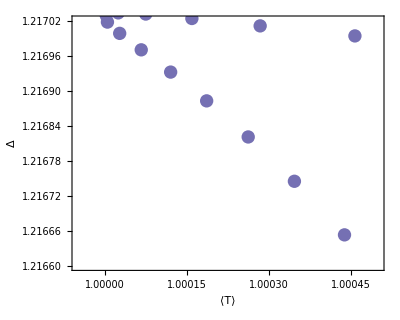

```mathematica
gaptracedelta =ListPlot[gapVtrace24,PlotStyle->{RGBColor["#7570b3"],PointSize->0.024},Frame->{True,True},FrameTicks->{{Automatic,None},{Automatic,None}},LabelStyle->{FontFamily->"Times New Roman",FontSize->15,Black},AspectRatio->0.8,PlotRange->{{0.9998,1.0095},{1.2166,1.21705}},FrameLabel->{Row[{"⟨",OverBar["T"],"⟩"}],"Δ"},FrameStyle->{Thickness[0.003],Black},Axes->False,]
gaptraceDeltainset = ListPlot[gapVtrace24,PlotStyle->{RGBColor["#7570b3"],PointSize->0.024},Frame->{True,True},FrameTicks->{{Automatic,None},{Automatic,None}},LabelStyle->{FontFamily->"Times New Roman",FontSize->6,Black},AspectRatio->0.8,PlotRange->{{0.99995,1.0005},{1.2166,1.21702}},FrameLabel->{Row[{"⟨",OverBar["T"],"⟩"}],"Δ"},FrameStyle->{Thickness[0.003],Black},Axes->False]
```

```mathematica
Export["~/Dropbox/quartic/manuscript/gap-v-trace-delta.pdf",gaptracedelta]
```

~/Dropbox/quartic/manuscript/gap-v-trace-delta.pdf

```mathematica
rmsBtable=Table[{d,Abs@rmsCurvature[{"QHofstadter",1,24,d}]},{d,-0.3,0.05,0.01}]
rmsGtable=Table[{d,Abs@trRMSMetric[{"QHofstadter",1,24,d}]},{d,-0.3,0.05,0.01}]
```

```mathematica
gapVrmsB24=MapThread[{#1,#2}&,{Drop[Transpose[rmsBtable][[2]],-2],Transpose[gapVsDelta24][[2]]}]
gapVrmsG24=MapThread[{#1,#2}&,{Drop[Transpose[rmsBtable][[2]],-2],Transpose[gapVsDelta24][[2]]}]
```

Butterfly plot

```mathematica
evalsVsFluxQFull=
Map[Tuples,Table[{{#/m},Sort@Eigenvalues[H[{0,0},{"QHofstadter",#,m,-0.25}]]},{m,3,80}]]&/@Range[1,80];
qButterfly2=ListPlot[Flatten[evalsVsFluxQFull,2],PlotRange->{{0,1},{-3.12,5.0}},AspectRatio->1,Frame->True,PlotStyle->{Black,PointSize->0.0015},LabelStyle->{20,FontFamily->"Times New Roman",Black},FrameTicks->{{{-3,-2,-1,0,1,2,3,4,5},None},{{0,1/2,1},None}},FrameLabel->{Row[{ϕ,"/",Subscript[ϕ,0]}],Row[{"E","/",Subscript[t,1]}]},RotateLabel->True,GridLines->None,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]]]
butterflyRaster1200=Rasterize[qButterfly2,RasterSize->1200,ImageSize->400]
butterflyRaster1500=Rasterize[qButterfly2,RasterSize->1500,ImageSize->400]
Export["/Users/dbauer/q-butterfly-raster-1200.pdf",butterflyRaster1200]
Export["/Users/dbauer/q-butterfly-raster-1500.pdf",butterflyRaster1500]
```

```mathematica
ClearAll[traceDelta]
traceDelta[m_] := traceDelta[m]= Quiet@ParallelTable[{t2,bzIntegrate[trGInequality,{"QHofstadter",1,m,t2}]/(2Pi m)},{t2,-0.25,0.0,0.01}]
```

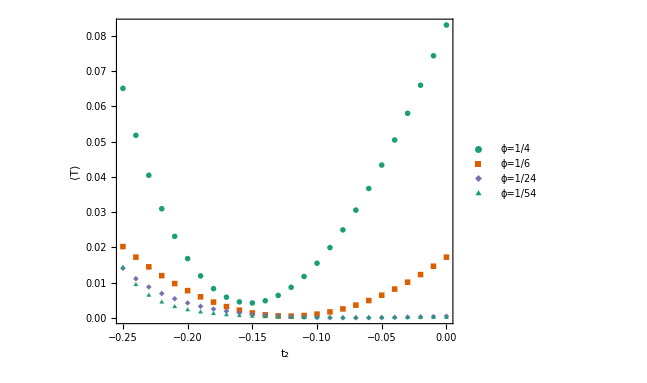

```mathematica
traceDeltaPlot=ListPlot[{traceDelta[4],traceDelta[6],traceDelta[24],traceDelta[54]},Joined->False,PlotStyle->{{PointSize->0.02,RGBColor["#1b9e77"],Joined->True},
{RGBColor["#d95f02"]},{RGBColor["#7570b3"]}},AspectRatio->0.8,PlotMarkers->{Automatic,Medium},PlotLegends->Placed[{"ϕ=1/4","ϕ=1/6","ϕ=1/24","ϕ=1/54"},{0.6,0.7}],LabelStyle->{FontSize->16,FontFamily->"Times New Roman"},AspectRatio->1,PlotRange->All,FrameLabel->{Subscript[t,2],"⟨T⟩"},Frame->{{True,True},{True,True}},FrameStyle->Directive[Black,Thickness[0.003]],FrameTicks->{{Automatic,None},{Automatic,None}}]
```

```mathematica
Export["~/Dropbox/quartic/manuscript/trace-delta-plot-new.pdf",traceDeltaPlot]
```

~/Dropbox/quartic/manuscript/trace-delta-plot-new.pdf

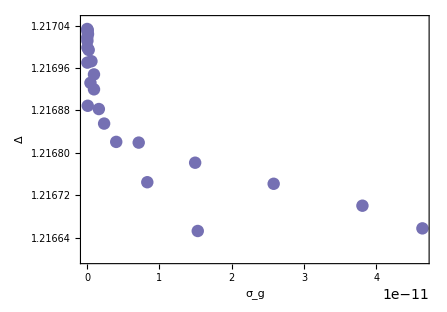

```mathematica
gapvrmsBdelta =ListPlot[gapVrmsB,PlotStyle->{RGBColor["#7570b3"],PointSize->0.02},Frame->{True,True},FrameTicks->{{Automatic,None},{Automatic,None}},LabelStyle->{FontFamily->"Times New Roman",FontSize->15,Black},AspectRatio->0.7,PlotRange->{Automatic,{1.2166,1.21705}},FrameLabel->{Subscript[σ,g],"Δ"},FrameStyle->{Thickness[0.003],Black},Axes->False]
```

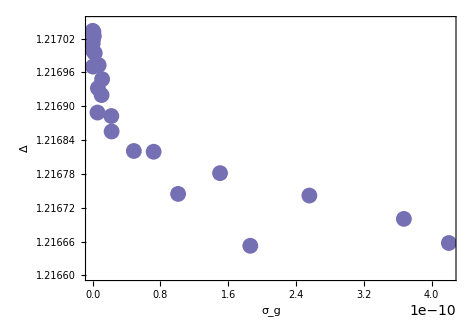

```mathematica
gapvrmsGdelta =ListPlot[gapVrmsG,PlotStyle->{RGBColor["#7570b3"],PointSize->0.024},Frame->{True,True},FrameTicks->{{Automatic,None},{Automatic,None}},LabelStyle->{FontFamily->"Times New Roman",FontSize->15,Black},AspectRatio->0.7,PlotRange->{Automatic,{1.2166,1.21705}},FrameLabel->{Subscript[σ,g],"Δ"},FrameStyle->{Thickness[0.003],Black},Axes->False]
```

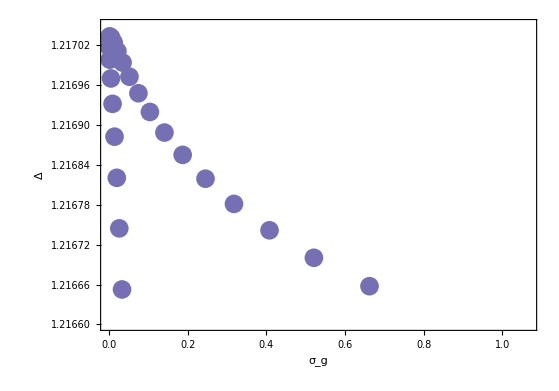

```mathematica
gapvrmsGdelta =ListPlot[gapVdetIneq,PlotStyle->{RGBColor["#7570b3"],PointSize->0.024},Frame->{True,True},FrameTicks->{{Automatic,None},{Automatic,None}},LabelStyle->{FontFamily->"Times New Roman",FontSize->15,Black},AspectRatio->0.7,PlotRange->{Automatic,{1.2166,1.21705}},FrameLabel->{Subscript[σ,g],"Δ"},FrameStyle->{Thickness[0.003],Black},Axes->False]
```

```mathematica
(*Fluctuations*)
quarticBZAmp[fn_,n_]:=
4n^2*Abs@NIntegrate[
	fn[{x,y},{"QHofstadter",1,n,-0.25}](Cos[2Pi*n*x]+Cos[2Pi*n*y]),
	{x,0,1/(2n)},{y,0,1/(2n)},
	AccuracyGoal->12,
	PrecisionGoal->4,
	MaxRecursion->9,
	Method->{"GlobalAdaptive","SymbolicProcessing"->0}
];

quarticBZRMS[fn_,n_]:=
With[{
mean=4n^2*NIntegrate[
	fn[{x,y},{"QHofstadter",1,n,-0.25}],
	{x,0,1/(2n)},{y,0,1/(2n)},
	AccuracyGoal->12,
	PrecisionGoal->4,
	MaxRecursion->9,
	Method->{"GlobalAdaptive","SymbolicProcessing"->0}
]},
2n*Sqrt@NIntegrate[
	(fn[{x,y},{"QHofstadter",1,n,-0.25}]-mean)^2,
	{x,0,1/(2n)},{y,0,1/(2n)},
	AccuracyGoal->12,
	PrecisionGoal->4,
	MaxRecursion->9,
	Method->{"GlobalAdaptive","SymbolicProcessing"->0}
]];
quarticBZRMS2[fn_,n_]:=
With[{
mean=4n^2*NIntegrate[
	fn[{x,y},{"QHofstadter",1,n,-0.02}],
	{x,0,1/(2n)},{y,0,1/(2n)},
	AccuracyGoal->12,
	PrecisionGoal->4,
	MaxRecursion->9,
	Method->{"GlobalAdaptive","SymbolicProcessing"->0}
]},
2n*Sqrt@NIntegrate[
	(fn[{x,y},{"QHofstadter",1,n,-0.02}]-mean)^2,
	{x,0,1/(2n)},{y,0,1/(2n)},
	AccuracyGoal->12,
	PrecisionGoal->4,
	MaxRecursion->9,
	Method->{"GlobalAdaptive","SymbolicProcessing"->0}
]];
Clear[hofBZRMS]
hofBZRMS[fn_,n_]:=
With[{
mean=4n^2*NIntegrate[
	fn[{x,y},{"Hofstadter",1,n}],
	{x,0,1/(2n)},{y,0,1/(2n)},
	AccuracyGoal->12,
	PrecisionGoal->4,
	MaxRecursion->9,
	Method->{"GlobalAdaptive","SymbolicProcessing"->0}
]},
2n*Sqrt@NIntegrate[
	(fn[{x,y},{"Hofstadter",1,n}]-mean)^2,
	{x,0,1/(2n)},{y,0,1/(2n)},
	AccuracyGoal->12,
	PrecisionGoal->4,
	MaxRecursion->9,
	Method->{"GlobalAdaptive","SymbolicProcessing"->0}
]];
anisoBZRMS[fn_,n_]:=
With[{
mean=4n^2*NIntegrate[
	fn[{x,y},{"p2x4",1,n,-0.25}],
	{x,0,1/(2n)},{y,0,1/(2n)},
	AccuracyGoal->12,
	PrecisionGoal->4,
	MaxRecursion->9,
	Method->{"GlobalAdaptive","SymbolicProcessing"->0}
]},
2n*Sqrt@NIntegrate[
	(fn[{x,y},{"p2x4",1,n,-0.25}]-mean)^2,
	{x,0,1/(2n)},{y,0,1/(2n)},
	AccuracyGoal->12,
	PrecisionGoal->4,
	MaxRecursion->9,
	Method->{"GlobalAdaptive","SymbolicProcessing"->0}
]];
```

```mathematica
quarticBZAmp[trG,4]
```

8.90613

```mathematica
Table[{n,anisoBZRMS[curvature,n]},{n,4,30}]
```

{{4,12.0541},{5,4.79147},{6,2.64798},{7,1.79124},{8,1.8206},{9,2.01855},{10,2.10914},{11,2.09572},{12,2.03418},{13,1.95662},{14,1.87425},{15,1.79074},{16,1.70812},{17,1.62793},{18,1.55122},{19,1.4785},{20,1.40998},{21,1.34564},{22,1.28535},{23,1.22893},{24,1.17613},{25,1.12674},{26,1.0805},{27,1.03719},{28,0.996594},{29,0.958501},{30,0.922721}}

```mathematica
Table[{n,quarticBZAmp[curvature,n]},{n,4,13}]
```

{{4,8.90613},{5,9.036},{6,4.41742},{7,0.917331},{8,0.401157},{9,0.471873},{10,0.224813},{11,0.0491058},{12,0.0128809},{13,0.0173236}}

```mathematica
Table[{n,quarticBZAmp[trG,n]},{n,14,20}]
```

{{14,0.00823945},{15,0.00184567},{16,0.000368849},{17,0.000548288},{18,0.000261448},{19,0.0000594743},{20,9.96915×10^-6}}

```mathematica
Table[{n,quarticBZRMS[trG,n]},{n,4,13}]
```

{{4,9.02028},{5,9.14665},{6,4.42434},{7,0.917332},{8,0.401158},{9,0.471876},{10,0.224814},{11,0.0491058},{12,0.0128809},{13,0.0173236}}

```mathematica
quarticRMSB = Table[{n,quarticBZRMS[curvature,n]},{n,4,35}]
hofRMSB = Table[{n,hofBZRMS[curvature,n]},{n,4,35}]
anisoRMSB = Table[{n,anisoBZRMS[curvature,n]},{n,4,35}]
quarticRMSB2 = Table[{n,quarticBZRMS2[curvature,n]},{n,4,35}]
```

{{4,9.14757},{5,9.48281},{6,4.74732},{7,1.1094},{8,0.340546},{9,0.476275},{10,0.242384},{11,0.0602091},{12,0.00919419},{13,0.0171852},{14,0.00888199},{15,0.00227909},{16,0.000219469},{17,0.000536385},{18,0.000281428},{19,0.0000737647},{20,4.89665×10^-6},{21,0.0000154655},{22,8.21782×10^-6},{23,2.18716×10^-6},{24,1.04058×10^-7},{25,4.24093×10^-7},{26,2.27704×10^-7},{27,6.13066×10^-8},{28,2.11848×10^-9},{29,1.12297×10^-8},{30,6.083×10^-9},{31,1.6501×10^-9},{32,4.09037×10^-11},{33,2.88597×10^-10},{34,1.56011×10^-10},{35,4.22949×10^-11}}

{{4,10.9248},{5,5.87698},{6,2.92659},{7,1.35738},{8,0.596171},{9,0.251164},{10,0.102416},{11,0.0406802},{12,0.0158136},{13,0.00603727},{14,0.00226986},{15,0.000842242},{16,0.000308955},{17,0.000112194},{18,0.0000403858},{19,0.000014423},{20,5.11455×10^-6},{21,1.80213×10^-6},{22,6.31329×10^-7},{23,2.20007×10^-7},{24,7.63004×10^-8},{25,2.63443×10^-8},{26,9.0584×10^-9},{27,3.10241×10^-9},{28,1.05976×10^-9},{29,3.60206×10^-10},{30,1.23215×10^-10},{31,4.37394×10^-11},{32,1.62563×10^-11},{33,9.91739×10^-12},{34,4.60865×10^-12},{35,3.72299×10^-12}}

{{4,11.1502},{5,7.23408},{6,3.50862},{7,1.71468},{8,0.93125},{9,0.459769},{10,0.21282},{11,0.101078},{12,0.0476874},{13,0.0217765},{14,0.00986953},{15,0.00446673},{16,0.00199801},{17,0.000885538},{18,0.000390825},{19,0.000171518},{20,0.000074827},{21,0.0000325015},{22,0.0000140624},{23,6.06009×10^-6},{24,2.60232×10^-6},{25,1.11403×10^-6},{26,4.75507×10^-7},{27,2.02406×10^-7},{28,8.59424×10^-8},{29,3.6407×10^-8},{30,1.53891×10^-8},{31,6.49209×10^-9},{32,2.73341×10^-9},{33,1.14866×10^-9},{34,4.82471×10^-10},{35,2.02063×10^-10}}

{{4,9.70658},{5,4.96673},{6,2.33245},{7,1.0179},{8,0.420432},{9,0.166545},{10,0.0638507},{11,0.0238444},{12,0.00871426},{13,0.00312778},{14,0.00110557},{15,0.000385675},{16,0.000132997},{17,0.0000454099},{18,0.0000153677},{19,5.15989×10^-6},{20,1.72027×10^-6},{21,5.69883×10^-7},{22,1.87699×10^-7},{23,6.14976×10^-8},{24,2.00532×10^-8},{25,6.51051×10^-9},{26,2.10571×10^-9},{27,6.78079×10^-10},{28,2.17601×10^-10},{29,6.96427×10^-11},{30,2.13244×10^-11},{31,4.82383×10^-12},{32,2.59965×10^-12},{33,9.94926×10^-13},{34,8.20741×10^-13},{35,8.62643×10^-13}}

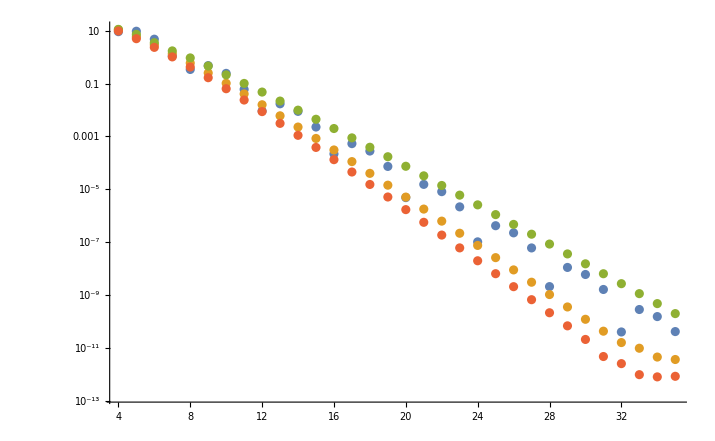

```mathematica
ListLogPlot[{quarticRMSB,hofRMSB,anisoRMSB,quarticRMSB2},PlotRange->All]
```

```mathematica
anisoRMS = {{4,12.05405709801912},{5,4.791471295304913},{6,2.647977681208338},{7,1.7912407225035367},{8,1.820603606992577},{9,2.0185471248537428},{10,2.1091400211992464},{11,2.095724864202582},{12,2.034180528210147},{13,1.9566183788214206},{14,1.8742506369620384},{15,1.7907363152591589},{16,1.708115528685222},{17,1.6279341102816023},{18,1.5512164508872275},{19,1.4784999238750858},{20,1.4099785646507605},{21,1.3456394275024326},{22,1.285352820875944},{23,1.2289255655254823},{24,1.1761326288617455},{25,1.1267366279993865},{26,1.0804999768465426},{27,1.0371922565042357},{28,0.9965944370529173},{29,0.958501053602809},{30,0.9227210799707845}}
```

{{4,12.0541},{5,4.79147},{6,2.64798},{7,1.79124},{8,1.8206},{9,2.01855},{10,2.10914},{11,2.09572},{12,2.03418},{13,1.95662},{14,1.87425},{15,1.79074},{16,1.70812},{17,1.62793},{18,1.55122},{19,1.4785},{20,1.40998},{21,1.34564},{22,1.28535},{23,1.22893},{24,1.17613},{25,1.12674},{26,1.0805},{27,1.03719},{28,0.996594},{29,0.958501},{30,0.922721}}

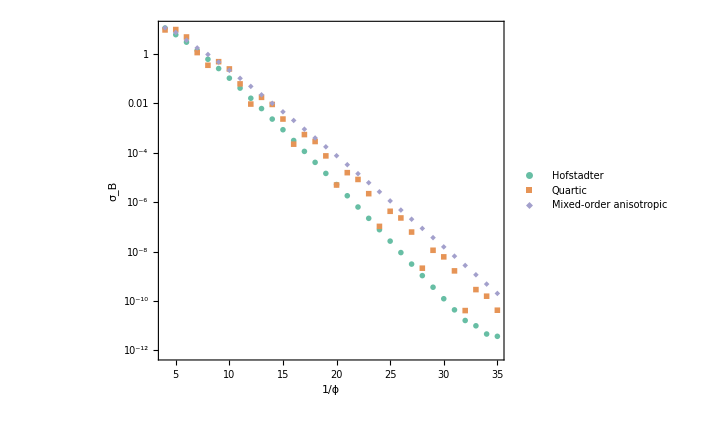

```mathematica
rmsFluctPlot=ListLogPlot[{hofRMSB,quarticRMSB,anisoRMSB},Joined->False,PlotStyle->{{PointSize->0.02,Lighter@RGBColor["#1b9e77"],Joined->True},
{Lighter@RGBColor["#d95f02"]},{Lighter@RGBColor["#7570b3"]}},AspectRatio->0.8,PlotMarkers->{Automatic,Medium},PlotLegends->Placed[{"Hofstadter","Quartic","Mixed-order anisotropic"},{0.3,0.3}],LabelStyle->{FontSize->16,FontFamily->"Times New Roman"},PlotRange->All,FrameLabel->{Row[{1,"/",ϕ}],Subscript[σ,B]},Frame->{{True,True},{True,True}},FrameStyle->Directive[Black,Thickness[0.003]],FrameTicks->{{Automatic,None},{Automatic,None}},AspectRatio->0.7]
```

```mathematica
Export["~/Dropbox/quartic/manuscript/rms-curv-fluct.pdf",rmsFluctPlot]
```

~/Dropbox/quartic/manuscript/rms-curv-fluct.pdf

```mathematica
traceAniso[m_] := traceAniso[m]= Quiet@ParallelTable[{t2,bzIntegrate[trGInequality,{"p2x4",1,m,t2}]/(2Pi m)},{t2,-0.25,0.0,0.01}]
```

```mathematica
bandEnergy[{k1,k2},{"p2x4",1,10,0},1]
```

```mathematica
Table[{n,chernNumber[{"p2x4",1,n,-0.25}]},{n,4,}]
```

{{4,-4.},{5,-3.57053},{6,-3.81202},{7,-3.97164},{8,-4.07777}}

```mathematica
chernNumber[{"p2x4",1,10,-0.25}]
```

-9.99999

```mathematica
Table[{n,chernNumber[{"p2x4",1,n,-0.25}]},{n,4,35}]
```

{{4,-4.},{5,-5.},{6,-6.},{7,-6.99997},{8,-8.},{9,-9.},{10,-9.99999},{11,-11.},{12,-12.0012},{13,-13.},{14,-14.},{15,-15.},{16,-16.},{17,-17.},{18,-18.},{19,-19.},{20,-20.},{21,-21.},{22,-22.},{23,-23.},{24,-24.},{25,-25.},{26,-26.},{27,-27.},{28,-28.},{29,-29.},{30,-30.},{31,-31.},{32,-32.},{33,-33.},{34,-34.},{35,-35.}}

```mathematica
bandGeometryTable[model_,m_] := Quiet@ParallelTable[{m,ToString@SetPrecision[t2,2],Abs@rmsCurvature[{model,1,m,t2}],

Abs@rmsTrG[{model,1,m,t2}],bzIntegrate[trGInequality,{model,1,m,t2}]/(2Pi m),bzIntegrate[detGInequality,{model,1,m,t2}]/(2Pi m)},{t2,-0.25,0,0.01}]
```

```mathematica
quarticBG=Join[{{"UCarea","t2","rmsB","rmsTrace","traceIneq","detIneq"}},bandGeometryTable["QHofstadter",6],bandGeometryTable["QHofstadter",24],bandGeometryTable["QHofstadter",54]]
```

{{UCarea,t2,rmsB,rmsTrace,traceIneq,detIneq},{6,-0.25,0.120251,4.42433,0.0202072,0.3047},{6,-0.24,0.112183,4.1544,0.0172054,0.257392},{6,-0.23,0.104141,3.88155,0.0144552,0.214255},{6,-0.22,0.0961257,3.60578,0.0119558,0.175255},{6,-0.21,0.0881357,3.32712,0.00970598,0.140358},{6,-0.20,0.0801723,3.04559,0.00770476,0.109532},{6,-0.19,0.0722342,2.7612,0.00595083,0.0827476},{6,-0.18,0.0643216,2.47397,0.00444283,0.0599738},{6,-0.17,0.0564341,2.18391,0.00317927,0.041183},{6,-0.16,0.0485716,1.89104,0.00215856,0.0263483},{6,-0.15,0.0407338,1.59537,0.00137901,0.0154444},{6,-0.14,0.0329203,1.29692,0.000838841,0.00844734},{6,-0.13,0.0251309,0.995696,0.000536155,0.00533447},{6,-0.12,0.0173652,0.691709,0.000468977,0.00608468},{6,-0.11,0.00962267,0.384974,0.00063524,0.0106783},{6,-0.1,0.0019033,0.0755036,0.00103279,0.019097},{6,-0.090,0.00579389,0.236706,0.0016594,0.0313238},{6,-0.080,0.0134689,0.551626,0.00251276,0.0473434},{6,-0.070,0.0211222,0.869255,0.00359048,0.0671415},{6,-0.060,0.0287544,1.18958,0.0048901,0.0907056},{6,-0.050,0.0363659,1.5126,0.00640912,0.118024},{6,-0.040,0.0439573,1.83831,0.00814495,0.149087},{6,-0.030,0.051529,2.16668,0.010095,0.183886},{6,-0.020,0.0590815,2.49773,0.0122564,0.222412},{6,-0.01,0.0666155,2.83143,0.0146267,0.26466},{6,0,0.0741314,3.16778,0.0172028,0.310625},{24,-0.25,3.1479×10^-9,3.10477×10^-7,0.0140393,1.06597},{24,-0.24,5.60628×10^-9,1.04891×10^-7,0.0110846,0.84039},{24,-0.23,6.99669×10^-9,2.10558×10^-7,0.00874655,0.662359},{24,-0.22,5.74485×10^-9,1.94029×10^-7,0.00688563,0.520951},{24,-0.21,3.89234×10^-9,1.40095×10^-7,0.00539806,0.408103},{24,-0.20,2.25371×10^-9,8.53306×10^-8,0.00420565,0.317766},{24,-0.19,1.07573×10^-9,4.30917×10^-8,0.00324872,0.245346},{24,-0.18,3.5376×10^-10,1.57887×10^-8,0.00248117,0.187308},{24,-0.17,1.23559×10^-11,1.14249×10^-9,0.00186703,0.140902},{24,-0.16,1.42507×10^-10,4.61362×10^-9,0.00137798,0.103969},{24,-0.15,1.42072×10^-10,5.16658×10^-9,0.00099151,0.0747952},{24,-0.14,8.89695×10^-11,3.42768×10^-9,0.000689592,0.0520119},{24,-0.13,3.20759×10^-11,1.32991×10^-9,0.000457681,0.0345162},{24,-0.12,4.90443×10^-12,1.16969×10^-10,0.000283965,0.0214135},{24,-0.11,1.71561×10^-11,6.40933×10^-10,0.000158791,0.0119735},{24,-0.1,1.16054×10^-11,4.5812×10^-10,0.0000742239,0.00559656},{24,-0.090,3.3184×10^-13,2.34338×10^-11,0.0000237101,0.00178772},{24,-0.080,5.70146×10^-12,2.22759×10^-10,1.80741×10^-6,0.000136276},{24,-0.070,1.99378×10^-12,8.19997×10^-11,3.97786×10^-6,0.000299924},{24,-0.060,5.25194×10^-12,2.1089×10^-10,0.0000264215,0.00199216},{24,-0.050,4.46059×10^-12,1.81973×10^-10,0.0000659443,0.00497225},{24,-0.040,6.86683×10^-11,2.8402×10^-9,0.000119852,0.00903718},{24,-0.030,2.43804×10^-10,1.0188×10^-8,0.000185865,0.0140152},{24,-0.020,6.06584×10^-10,2.55787×10^-8,0.000262049,0.0197606},{24,-0.01,1.25491×10^-9,5.33571×10^-8,0.000346756,0.0261493},{24,0,2.3082×10^-9,9.88984×10^-8,0.000438582,0.0330756},{54,-0.25,5.41765×10^-13,2.12543×10^-11,0.0143172,2.44624},{54,-0.24,1.25384×10^-13,5.07967×10^-12,0.0093725,1.59746},{54,-0.23,2.98472×10^-13,1.17768×10^-11,0.00635963,1.08232},{54,-0.22,1.92898×10^-13,7.51683×10^-12,0.00442327,0.75205},{54,-0.21,1.61233×10^-13,6.36561×10^-12,0.00312826,0.531528},{54,-0.20,1.75794×10^-13,6.90389×10^-12,0.00223567,0.379697},{54,-0.19,1.21888×10^-13,4.83927×10^-12,0.00160618,0.272701},{54,-0.18,1.20297×10^-14,6.79193×10^-13,0.00115455,0.195977},{54,-0.17,8.89418×10^-14,3.47225×10^-12,0.000826479,0.140267},{54,-0.16,6.71549×10^-14,2.60588×10^-12,0.000586251,0.0994842},{54,-0.15,6.75303×10^-14,2.64395×10^-12,0.000409671,0.0695133},{54,-0.14,3.88319×10^-14,1.52365×10^-12,0.000279963,0.0475012},{54,-0.13,6.64386×10^-14,2.61902×10^-12,0.000185246,0.0314292},{54,-0.12,8.2074×10^-14,3.20835×10^-12,0.000116957,0.0198424},{54,-0.11,5.83864×10^-14,2.28385×10^-12,0.0000688183,0.0116752},{54,-0.1,1.04042×10^-13,4.11569×10^-12,0.0000361703,0.00613625},{54,-0.090,5.93429×10^-14,2.344×10^-12,0.0000155067,0.00263066},{54,-0.080,7.57561×10^-14,2.98058×10^-12,4.16186×10^-6,0.000706044},{54,-0.070,6.28285×10^-14,2.47254×10^-12,8.9235×10^-8,0.0000151384},{54,-0.060,6.88546×10^-14,2.7381×10^-12,1.70383×10^-6,0.000289047},{54,-0.050,6.97743×10^-14,2.75051×10^-12,7.76875×10^-6,0.00131794},{54,-0.040,7.203×10^-14,2.82525×10^-12,0.0000173122,0.00293698},{54,-0.030,4.06084×10^-14,1.60187×10^-12,0.0000295662,0.00501586},{54,-0.020,5.26765×10^-14,2.07974×10^-12,0.0000439205,0.00745109},{54,-0.01,3.81717×10^-14,1.50007×10^-12,0.000059888,0.0101601},{54,0,2.08808×10^-13,8.25639×10^-12,0.0000770787,0.0130766}}

```mathematica
Export["~/Dropbox/quartic/June 2018/Many-body code/quartic-geometry-data.csv",quarticBG]
```

~/Dropbox/quartic/June 2018/Many-body code/quartic-geometry-data.csv

```mathematica
mixedAnisoBG=Join[{{"UCarea","t2","rmsB","rmsTrace","traceIneq","detIneq"}},bandGeometryTable["p2x4",6],bandGeometryTable["p2x4",24],bandGeometryTable["p2x4",54]];
```

```mathematica
Export["~/Dropbox/quartic/June 2018/Many-body code/mixed-aniso-geometry-data.csv",mixedAnisoBG]
```

~/Dropbox/quartic/June 2018/Many-body code/mixed-aniso-geometry-data.csv

```mathematica
quarticBG96=Join[{{"UCarea","t2","rmsB","rmsTrace","traceIneq","detIneq"}},bandGeometryTable["QHofstadter",96]]
Export["~/Dropbox/quartic/June 2018/Many-body code/quartic-geometry-data-96.csv",quarticBG96]
```

{{UCarea,t2,rmsB,rmsTrace,traceIneq,detIneq},{96,-0.25,1.21189×10^-12,4.95119×10^-11,0.0143925,4.3719},{96,-0.24,2.21828×10^-12,8.72952×10^-11,0.0074053,2.24165},{96,-0.23,1.03234×10^-12,4.07434×10^-11,0.00427631,1.29246},{96,-0.22,4.03117×10^-13,1.60691×10^-11,0.00264935,0.800085},{96,-0.21,2.67496×10^-13,1.05115×10^-11,0.00171774,0.518503},{96,-0.20,1.55219×10^-13,6.36934×10^-12,0.00114755,0.34629},{96,-0.19,1.27947×10^-13,5.00078×10^-12,0.000781453,0.235773},{96,-0.18,2.33423×10^-13,9.19673×10^-12,0.000538006,0.162303},{96,-0.17,3.71691×10^-13,1.46617×10^-11,0.000371895,0.112182},{96,-0.16,1.65445×10^-13,6.44303×10^-12,0.000256448,0.0773527},{96,-0.15,8.6333×10^-14,3.52149×10^-12,0.000175233,0.0528537},{96,-0.14,2.5482×10^-13,1.0011×10^-11,0.000117741,0.0355121},{96,-0.13,1.93598×10^-13,7.74961×10^-12,0.0000770357,0.0232343},{96,-0.12,2.88064×10^-13,1.14036×10^-11,0.0000484146,0.0146019},{96,-0.11,1.48959×10^-13,5.88911×10^-12,0.000028619,0.0086314},{96,-0.1,1.19863×10^-13,4.60884×10^-12,0.0000153442,0.00462775},{96,-0.090,1.99967×10^-13,7.90549×10^-12,6.9335×10^-6,0.0020911},{96,-0.080,2.22194×10^-13,8.77133×10^-12,2.17744×10^-6,0.0006567},{96,-0.070,2.9092×10^-13,1.15186×10^-11,1.8208×10^-7,0.0000549141},{96,-0.060,1.52114×10^-13,5.96268×10^-12,2.79005×10^-7,0.0000841458},{96,-0.050,1.16568×10^-13,4.65914×10^-12,1.96347×10^-6,0.000592168},{96,-0.040,1.77888×10^-13,7.01496×10^-12,4.85102×10^-6,0.00146304},{96,-0.030,1.48711×10^-13,5.8125×10^-12,8.64665×10^-6,0.00260778},{96,-0.020,1.33563×10^-13,5.22209×10^-12,0.0000131225,0.00395768},{96,-0.01,1.5436×10^-13,6.10204×10^-12,0.0000181017,0.00545938},{96,0,4.55077×10^-13,1.79082×10^-11,0.0000234461,0.00707126}}

~/Dropbox/quartic/June 2018/Many-body code/quartic-geometry-data-96.csv

```mathematica
bosonBG=Join[{{"UCarea","t2","rmsB","rmsTrace","traceIneq","detIneq"}},bandGeometryTable["QHofstadter",9],bandGeometryTable["QHofstadter",16],bandGeometryTable["QHofstadter",25],bandGeometryTable["QHofstadter",36],
bandGeometryTable["QHofstadter",49],bandGeometryTable["QHofstadter",64],bandGeometryTable["QHofstadter",81]];
```

```mathematica
Export["/home/bart/DiagHam_Stability/trunk/quartic_2/quartic-boson-geometry.csv",bosonBG]
```

~/Dropbox/quartic/June 2018/Many-body code/quartic-boson-geometry.csv

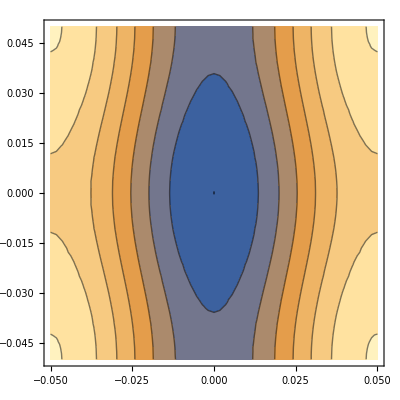

```mathematica
ContourPlot[Abs@metric11[{k1,k2},{"AnisoHofstadter",1,10,1}]/(2Pi *10),{k1,-1/(20),1/(20)},{k2,-1/(20),1/(20)}]
```

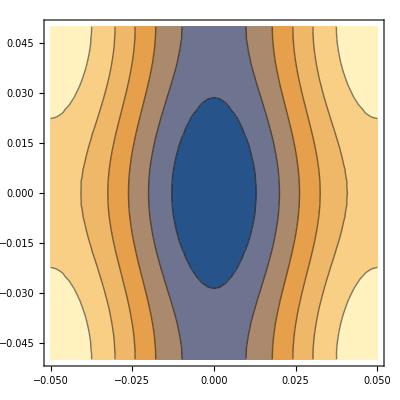

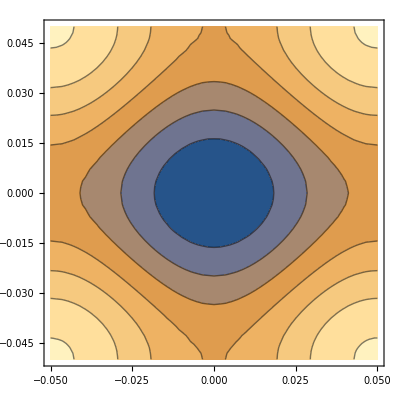

```mathematica
ContourPlot[Abs@metric11[{k1,k2},{"AnisoHofstadter",1,10,0.99}]/(2Pi *10),{k1,-1/(20),1/(20)},{k2,-1/(20),1/(20)}]
ContourPlot[trG[{k1,k2},{"AnisoHofstadter",1,10,0.99}]/(2Pi *10),{k1,-1/(20),1/(20)},{k2,-1/(20),1/(20)}]
```

```mathematica
bzIntegrate[metric11,{"AnisoHofstadter",1,10,0.99}]
```

31.1482

```mathematica
bzIntegrate[metric22,{"AnisoHofstadter",1,10,0.99}]
```

31.9102

```mathematica
Table[{α,bzIntegrate[metric11,{"AnisoHofstadter",1,10,α}]/(20Pi)},{α,0.8,1.2,0.01}]
```

{{0.8,0.383494},{0.81,0.389302},{0.82,0.395121},{0.83,0.40095},{0.84,0.406789},{0.85,0.412639},{0.86,0.4185},{0.87,0.424372},{0.88,0.430254},{0.89,0.436148},{0.9,0.442053},{0.91,0.44797},{0.92,0.453899},{0.93,0.459839},{0.94,0.465792},{0.95,0.471756},{0.96,0.477733},{0.97,0.483722},{0.98,0.489724},{0.99,0.495738},{1.,0.501766},{1.01,0.507806},{1.02,0.51386},{1.03,0.519926},{1.04,0.526007},{1.05,0.5321},{1.06,0.538208},{1.07,0.544329},{1.08,0.550464},{1.09,0.556614},{1.1,0.562777},{1.11,0.568956},{1.12,0.575148},{1.13,0.581356},{1.14,0.587578},{1.15,0.593828},{1.16,0.600079},{1.17,0.606346},{1.18,0.612629},{1.19,0.618936},{1.2,0.62525}}

```mathematica
Table[{α,bzIntegrate[metric22,{"AnisoHofstadter",1,10,α}]/(20Pi)},{α,0.8,1.2,0.01}]
```

{{0.8,0.657063},{0.81,0.6472},{0.82,0.637615},{0.83,0.628298},{0.84,0.619236},{0.85,0.61041},{0.86,0.601827},{0.87,0.593469},{0.88,0.585314},{0.89,0.577379},{0.9,0.569643},{0.91,0.562099},{0.92,0.554741},{0.93,0.54756},{0.94,0.54055},{0.95,0.533706},{0.96,0.527021},{0.97,0.52049},{0.98,0.514107},{0.99,0.507867},{1.,0.501766},{1.01,0.495798},{1.02,0.48996},{1.03,0.484246},{1.04,0.478654},{1.05,0.473178},{1.06,0.467816},{1.07,0.462564},{1.08,0.457418},{1.09,0.452375},{1.1,0.447432},{1.11,0.442586},{1.12,0.437834},{1.13,0.433174},{1.14,0.428602},{1.15,0.424116},{1.16,0.419714},{1.17,0.415393},{1.18,0.411151},{1.19,0.406986},{1.2,0.402895}}

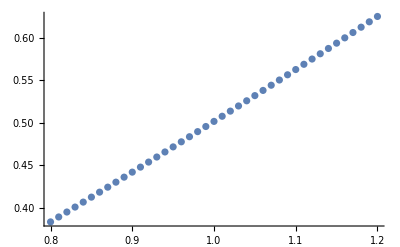

```mathematica
ListPlot[%26]
```

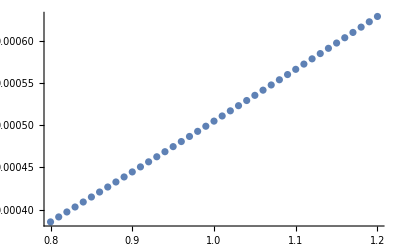

```mathematica
ListPlot[%31,PlotRange->All]
```

```mathematica
anisoTable =Table[{α,bzIntegrate[trGInequality,{"AnisoHofstadter",1,96,α}]/(96Pi)},{α,1.0,1.6,0.01}]
```

{{1.,0.0000468922},{1.01,0.00014925},{1.02,0.00045231},{1.03,0.00095023},{1.04,0.00163739},{1.05,0.0025084},{1.06,0.00355806},{1.07,0.00478136},{1.08,0.0061735},{1.09,0.00772985},{1.1,0.00944593},{1.11,0.0113174},{1.12,0.0133403},{1.13,0.0155103},{1.14,0.0178239},{1.15,0.0202771},{1.16,0.0228664},{1.17,0.0255884},{1.18,0.0284397},{1.19,0.0314171},{1.2,0.0345173},{1.21,0.0377375},{1.22,0.0410746},{1.23,0.0445259},{1.24,0.0480886},{1.25,0.05176},{1.26,0.0555377},{1.27,0.0594191},{1.28,0.0634017},{1.29,0.0674834},{1.3,0.0716617},{1.31,0.0759346},{1.32,0.0802999},{1.33,0.0847556},{1.34,0.0892996},{1.35,0.0939301},{1.36,0.0986451},{1.37,0.103443},{1.38,0.108321},{1.39,0.113279},{1.4,0.118315},{1.41,0.123426},{1.42,0.128612},{1.43,0.13387},{1.44,0.1392},{1.45,0.1446},{1.46,0.150069},{1.47,0.155604},{1.48,0.161205},{1.49,0.166871},{1.5,0.1726},{1.51,0.178391},{1.52,0.184243},{1.53,0.190154},{1.54,0.196124},{1.55,0.202151},{1.56,0.208235},{1.57,0.214374},{1.58,0.220567},{1.59,0.226814},{1.6,0.233112}}

```mathematica
Export["~/Dropbox/quartic/June 2018/Many-body code/ansio-trace.csv",anisoTable]
```

~/Dropbox/quartic/June 2018/Many-body code/ansio-trace.csv

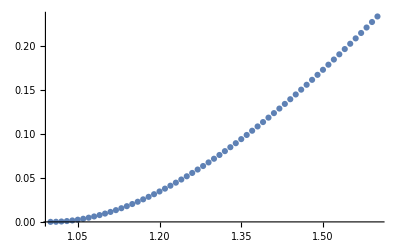

```mathematica
ListPlot[%4,PlotRange->All]
```

```mathematica
traceDeltaMixed[m_] := traceDeltaMixed[m]= Quiet@ParallelTable[{t2,bzIntegrate[trGInequality,{"p2x4",1,m,t2}]/(2Pi m)},{t2,-0.25,0.0,0.01}]
```

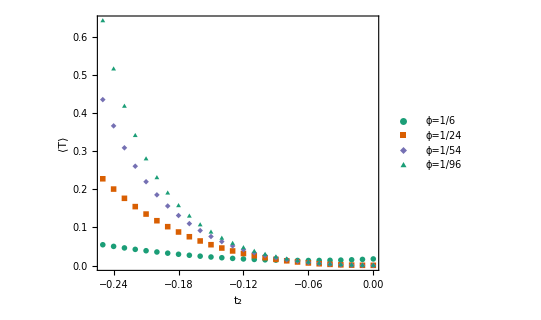

```mathematica
traceDeltaPlot=ListPlot[{traceDeltaMixed[6],traceDeltaMixed[24],traceDeltaMixed[54],traceDeltaMixed[96]},Joined->False,PlotStyle->{{PointSize->0.02,RGBColor["#1b9e77"],Joined->True},
{RGBColor["#d95f02"]},{RGBColor["#7570b3"]}},AspectRatio->0.8,PlotMarkers->{Automatic,Medium},PlotLegends->Placed[{"ϕ=1/6","ϕ=1/24","ϕ=1/54","ϕ=1/96"},{0.6,0.7}],LabelStyle->{FontSize->16,FontFamily->"Times New Roman"},AspectRatio->1,PlotRange->All,FrameLabel->{Subscript[t,2],"⟨T⟩"},Frame->{{True,True},{True,True}},FrameStyle->Directive[Black,Thickness[0.003]],FrameTicks->{{Automatic,None},{Automatic,None}}]
```

```mathematica
Table[{n,chernNumber[{"p2x4",1,6*n^2,-0.25}]},{n,10,15}]
```

Eigensystem::arh: Because finding 600 out of the 600 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

General::stop: Further output of Eigensystem :: arh will be suppressed during this calculation.

{{10,-600.},{11,-726.},{12,-864.},{13,-1014.},{14,-1176.},{15,-1350.}}

```mathematica
1.0/1350
```

0.000740741

```mathematica
Export["~/Dropbox/quartic/manuscript/trace-v-t2-mixed.pdf",traceDeltaPlot]
```

~/Dropbox/quartic/manuscript/trace-v-t2-mixed.pdf